## Compare this solution to ProofCircle.nb DeltaConfigurationSpacePolygon.nb Configuration Space for positioning two particles in a bounded polygon By Jingang Shi <13437170648@163.com>, Aaron Becker and Shiva Shahrokhi Try setting the polygon to be irregular, and dragging the vertices.

```mathematica
pnPoly::usage="pnPoly[{testx,testy},{{x1,y1},{x2,y2},...}] return true if {testx,testy} in inside polygon. 
  Polygon can be closed or not. A point will be inside exactly one member of a polygonal partitioning.
  C-code by W. Randolph Franklin (http://www.ecse.rpi.edu/Homepages/wrf/Research/Short_Notes/pnpoly.html).
  J. Wesenberg, 2008" ;

pnPoly[{testx_,testy_},pts_List]:=Xor@@((Xor[#⟦1,2⟧>testy,#⟦2,2⟧>testy]∧((testx-#⟦2,1⟧)<(#⟦1,1⟧-#⟦2,1⟧) (testy-#⟦2,2⟧)/(#⟦1,2⟧-#⟦2,2⟧)))&/@Partition[pts,2,1,{2,2}])

(*To make the point inside the polygon.  Assumes polygon contains {0,0} and is convex  DONE: replace NSolve*)
makeInPoly[stPt_,v_,vcopy_,sides_,center_]:=Module[{sl1,newptc=stPt},
Table[
If[pnPoly[stPt⟦i⟧,(#)&/@v]==False,
sl1 = {center,stPt⟦i⟧};
{If[SegmentIntersectionQ[{sl1,#}],newptc⟦i⟧ = LineIntersectionPoint2[{sl1,#}]];
}&/@Partition[.999vcopy,2,1](*TODO: I had to shrink this value because of instability if point exactly on the line*)
],{i,1,Length[stPt]}];(*end table for each point to force inside poly*)
If[newptc⟦1⟧==newptc⟦3⟧,newptc⟦1⟧=.09newptc⟦1⟧];(*the start points cannot be identical*)
newptc
];

(*To make the point inside the polygon*)
makeInPoly1[stPt_,v_,vcopy_,sides_,center_]:=Module[{newptc={},OriPt=stPt,ChanPt,i,ii,xx,yy},
For[i=1,i≤4,i++,
If[pnPoly[OriPt[[i]],(#)&/@v]==True,
AppendTo[newptc,OriPt[[i]]],

ChanPt={};
For[ii=1,ii≤sides∧ChanPt=={},ii++,
ChanPt=NSolve[{xx,yy}∈Line[{vcopy[[ii+1]],vcopy[[ii]]}]∧{xx,yy}∈Line[{center,OriPt[[i]]}],{xx,yy}]];
AppendTo[newptc,(1-0.001){xx,yy}/.Flatten[ChanPt]]
]
];(*end for*)
If[newptc[[1]]==newptc[[3]],newptc[[1]]=newptc[[1]]+{0.01,0.01}];(*the start points cannot be identical*)
newptc
];

(*return the third element of the crossproduct about two vectors in xOy*)
CrossTwoD[twoDvector1_,twoDvector2_]:=Cross[Append[twoDvector1,0],Append[twoDvector2,0]]⟦3⟧;

(*The parametric equation of the line containing the points a and b is a+γ (b-a), where 0≤γ≤1 for points between a and b. The value of γ is given by*)
γ[{a_,b_}][p_]:=((a-p).(a-b))/((a-b).(a-b))
(*for p on the line. For p not on the line, γ gives the closest point on the line.*)
(*Two lines, Subscript[L, 1] containing the points a and b with line Subscript[L, 2] containing the points c and d, intersect at a point ⟺ |{a-b,c-d}|≠0.  Compute the intersection point:*)
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
LineIntersectionPoint2[{{{ax_,ay_},{bx_,by_}},{{cx_,cy_},{dx_,dy_}}}]:={((-ay bx+ax by) (cx-dx)+(ax-bx) (cy dx-cx dy))/(-(ay-by) (cx-dx)+(ax-bx) (cy-dy)),((-ay bx+ax by) (cy-dy)+(ay-by) (cy dx-cx dy))/(-(ay-by) (cx-dx)+(ax-bx) (cy-dy))}
(*Use |{a-b,c-d}|≠0 along with the condition 0≤λ≤1 to determine whether two segments intersect:*)
SegmentIntersectionQ[{p1:{a_,b_},p2:{c_,d_}}]:=
If[Det[{a-b,c-d}]==0,False,
Module[{p=LineIntersectionPoint2[{p1,p2}]},0≤γ[p1][p]≤1∧0≤γ[p2][p]≤1]]

LineIntersectionPoint[{a_,b_},{c_,d_}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}];

(* a colored locator icon*)
loc[col_]:=ToExpression@GraphicsBox[{col,{AbsoluteThickness[1],Antialiasing->False,LineBox[{{{0,-10},{0,-2}},{{0,2},{0,10}},{{-10,0},{-2,0}},{{2,0},{10,0}}}],Antialiasing->True,CircleBox[{-0.5,0.5},5]},{AbsoluteThickness[3],Opacity[0.3],CircleBox[{-0.5,0.5},3]}},ImageSize->17,PlotRange->{{-8,8},{-8,8}}];

(*To get the boundary points of reachable sets*)
boundaryPt[sides_,vcopy_,ps2_,ps1_]:=Module[{xx,yy,i,j,ii,ps1Changed,ps2Changed,change,numLineInscpt1,numLineInscpt2,inscpt1,inscpt2,
intersectionP1={},intersectionP2={},preVReaSet={},vReaSetPt1={},vReaSetPt2={},TotalReaSet={}},

For[i=1,i≤sides,i++,
(*If the vector of the two start points is parallel with the ith side, add no reachable sets*)
If[-0.00001≤CrossTwoD[ps2-ps1,vcopy⟦i+1⟧-vcopy⟦i⟧]≤0.00001,AppendTo[TotalReaSet,{}],
intersectionP1={};
intersectionP2={};
(*To ensure the ps2Changed is closer to the ith side*)
If[(ps2-ps1).(vcopy⟦i+1⟧+vcopy⟦i⟧)/2<0,
{ps1Changed,ps2Changed}={ps2,ps1};change=1,
{ps1Changed,ps2Changed}={ps1,ps2};change=2];

(*To get the first intersection point of the line and the polygon*)
For[ii=1,ii≤sides∧intersectionP1=={},ii++,
intersectionP1=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii+1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt1=ii
];(*end for*)
inscpt1={xx,yy}/.Flatten[intersectionP1];

(*To get the second intersection point of the line and the polygon*)
For[ii=sides+1,ii≥2∧intersectionP2=={},ii--,
intersectionP2=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii-1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt2=ii
];(*end for*)
inscpt2={xx,yy}/.Flatten[intersectionP2];

(*To judge if there exists reachable set*)
If[(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]<0)
∨
(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]>0),
AppendTo[TotalReaSet,{}],

(*there exists reachable set*)
If[numLineInscpt1<i<numLineInscpt2,
If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt1=vcopy⟦i⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt2=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)],

If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt1=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt2=vcopy⟦i⟧-(ps2Changed-ps1Changed)]
];

(*To get all of the reachable points*)
preVReaSet={};vReaSetPt1={};vReaSetPt2={};
AppendTo[preVReaSet,inscpt1];
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP1]];
If[numLineInscpt1<i<numLineInscpt2,
For[j=numLineInscpt1+1,j≤numLineInscpt2-1,j++,AppendTo[preVReaSet,vcopy[[j]]]],
For[j=numLineInscpt1,j≥1,j--,AppendTo[preVReaSet,vcopy⟦j⟧]];For[j=sides,j≥numLineInscpt2,j--,AppendTo[preVReaSet,vcopy⟦j⟧]]
];(*end if*)
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP2]];
AppendTo[preVReaSet,inscpt2];

(*To get the vectors from start point(after the first move) to all of the other points*)
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt1,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt1)]];
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt2,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt2)]];

(*TotalReaSet includes all the coordinates of reachable sets*)
AppendTo[TotalReaSet,vReaSetPt1];
AppendTo[TotalReaSet,vReaSetPt2];
](*end if*)
];(*end if*)
];(*end for*)
TotalReaSet
];
calculateDeltaConfig[v_]:=Module[{vCF = {},i,j},
For[i=1,i≤Length[v],i++,
For[j=1,j≤Length[v],j++,
If[i+j==Length[v]∨i+j==2Length[v],
AppendTo[vCF,v⟦i⟧-v⟦Length[v]⟧  ],
AppendTo[vCF,v⟦i⟧-v⟦  QuotientRemainder[i+j,Length[v]]⟦2⟧  ⟧  ]
];
];
];(*end For*)
(*For[i=1,i≤Length[v],i++,
For[j=1,j≤Length[v],j++,
If[i+j==Length[v]∨i+j==2Length[v],
AppendTo[vCF,v⟦ Length[v]⟧  -v⟦i⟧ ],
AppendTo[vCF,v⟦  QuotientRemainder[i+j,Length[v]]⟦2⟧  ⟧ -v⟦i⟧ ]
];
];
];(*end For (flip the reachable set)*)*)
Return[MeshCoordinates[ConvexHullMesh[vCF]]]
]

deltaToTwoConfigs[vcopy_,ps2Mps1_]:=Module[{sides = Length[vcopy]-1,ps2,ps1},
For[i=1,i≤sides,i++,
(*place one particle at vertix*)
ps1 = 0.999*vcopy⟦i+1⟧;
ps2 = ps2Mps1+ps1;
If[ pnPoly[ps2,vcopy],Return[{ps2,ps1}]];
ps2 = 0.999*vcopy⟦i+1⟧;
ps1 = ps2-ps2Mps1;
If[ pnPoly[ps1,vcopy],Return[{ps2,ps1}]];
](*end FOR*)
] (*end module*)

boundaryPt2[vcopy_,ps2_,ps1_]:=Module[{xx,yy,i,j,ii,ps1Changed,ps2Changed,change,numLineInscpt1,numLineInscpt2,inscpt1,inscpt2,
intersectionP1={},intersectionP2={},preVReaSet={},vReaSetPt1={},vReaSetPt2={},TotalReaSet={},sides = Length[vcopy]-1
},
For[i=1,i≤sides,i++,
(*If the vector of the two start points is parallel with the ith side, add no reachable sets*)
If[-0.00001≤CrossTwoD[ps2-ps1,vcopy⟦i+1⟧-vcopy⟦i⟧]≤0.00001,AppendTo[TotalReaSet,{}],
intersectionP1={};
intersectionP2={};
(*To ensure the ps2Changed is closer to the ith side*)
If[(ps2-ps1).(vcopy⟦i+1⟧+vcopy⟦i⟧)/2<0,
{ps1Changed,ps2Changed}={ps2,ps1};change=1,
{ps1Changed,ps2Changed}={ps1,ps2};change=2];

(*To get the first intersection point of the line and the polygon*)
For[ii=1,ii≤sides∧intersectionP1=={},ii++,
intersectionP1=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii+1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt1=ii
];(*end for*)
inscpt1={xx,yy}/.Flatten[intersectionP1];

(*To get the second intersection point of the line and the polygon*)
For[ii=sides+1,ii≥2∧intersectionP2=={},ii--,
intersectionP2=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii-1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt2=ii
];(*end for*)
inscpt2={xx,yy}/.Flatten[intersectionP2];

(*To judge if there exists reachable set*)
If[(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]<0)
∨
(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]>0),
AppendTo[TotalReaSet,{}],

(*there exists reachable set*)
If[numLineInscpt1<i<numLineInscpt2,
If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt1=vcopy⟦i⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt2=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)],

If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt1=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt2=vcopy⟦i⟧-(ps2Changed-ps1Changed)]
];

(*To get all of the reachable points*)
preVReaSet={};vReaSetPt1={};vReaSetPt2={};
AppendTo[preVReaSet,inscpt1];
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP1]];
If[numLineInscpt1<i<numLineInscpt2,
For[j=numLineInscpt1+1,j≤numLineInscpt2-1,j++,AppendTo[preVReaSet,vcopy[[j]]]],
For[j=numLineInscpt1,j≥1,j--,AppendTo[preVReaSet,vcopy⟦j⟧]];For[j=sides,j≥numLineInscpt2,j--,AppendTo[preVReaSet,vcopy⟦j⟧]]
];(*end if*)
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP2]];
AppendTo[preVReaSet,inscpt2];

(*To get the vectors from start point(after the first move) to all of the other points*)
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt1,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt1)]];
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt2,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt2)]];

(*TotalReaSet includes all the coordinates of reachable sets*)
AppendTo[TotalReaSet,vReaSetPt1];
AppendTo[TotalReaSet,vReaSetPt2];
](*end if*)
];(*end if*)
];(*end for*)
TotalReaSet
];


boundaryPt3[vcopy_,ps2_,ps1_]:=Module[{xx,yy,i,j,ii,ps1Changed,ps2Changed,change,numLineInscpt1,numLineInscpt2,inscpt1,inscpt2,
intersectionP1={},intersectionP2={},preVReaSet={},vReaSetPt1={},vReaSetPt2={},TotalReaSet={},sides = Length[vcopy]-1
},
For[i=1,i≤sides,i++,
(*If the vector of the two start points is parallel with the ith side, add no reachable sets*)
If[-0.00001≤CrossTwoD[ps2-ps1,vcopy⟦i+1⟧-vcopy⟦i⟧]≤0.00001,AppendTo[TotalReaSet,{}],
intersectionP1={};
intersectionP2={};
(*To ensure the ps2Changed is closer to the ith side*)
If[(ps2-ps1).(vcopy⟦i+1⟧+vcopy⟦i⟧)/2<0,
{ps1Changed,ps2Changed}={ps2,ps1};change=1,
{ps1Changed,ps2Changed}={ps1,ps2};change=2];

(*To get the first intersection point of the line and the polygon*)
For[ii=1,ii≤sides∧intersectionP1=={},ii++,
intersectionP1=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii+1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt1=ii
];(*end for*)
inscpt1={xx,yy}/.Flatten[intersectionP1];

(*To get the second intersection point of the line and the polygon*)
For[ii=sides+1,ii≥2∧intersectionP2=={},ii--,
intersectionP2=NSolve[{xx,yy}∈InfiniteLine[{vcopy⟦i+1⟧-(ps2Changed-ps1Changed),vcopy⟦i⟧-(ps2Changed-ps1Changed)}]∧{xx,yy}∈Line[{vcopy⟦ii-1⟧,vcopy⟦ii⟧}],{xx,yy}];
numLineInscpt2=ii
];(*end for*)
inscpt2={xx,yy}/.Flatten[intersectionP2];

(*To judge if there exists reachable set*)
If[(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]<0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]<0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]<0)
∨
(CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]>0
∧CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]>0∧CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]>0),
AppendTo[TotalReaSet,{}],

(*there exists reachable set*)
If[numLineInscpt1<i<numLineInscpt2,
If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt1=vcopy⟦i⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt2=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)],

If[CrossTwoD[inscpt1-ps1Changed,vcopy⟦i+1⟧-ps2Changed]≤0,inscpt1=vcopy⟦i+1⟧-(ps2Changed-ps1Changed)];
If[CrossTwoD[inscpt2-ps1Changed,vcopy⟦i⟧-ps2Changed]≥0,inscpt2=vcopy⟦i⟧-(ps2Changed-ps1Changed)]
];

(*To get all of the reachable points*)
preVReaSet={};vReaSetPt1={};vReaSetPt2={};
AppendTo[preVReaSet,inscpt1];
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP1]];
If[numLineInscpt1<i<numLineInscpt2,
For[j=numLineInscpt1+1,j≤numLineInscpt2-1,j++,AppendTo[preVReaSet,vcopy[[j]]]],
For[j=numLineInscpt1,j≥1,j--,AppendTo[preVReaSet,vcopy⟦j⟧]];For[j=sides,j≥numLineInscpt2,j--,AppendTo[preVReaSet,vcopy⟦j⟧]]
];(*end if*)
AppendTo[preVReaSet,{xx,yy}/.Flatten[intersectionP2]];
AppendTo[preVReaSet,inscpt2];

(*To get the vectors from start point(after the first move) to all of the other points*)
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt1,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt1)]];
For[j=1,j≤Length[preVReaSet],j++,AppendTo[vReaSetPt2,ps2-ps1-(-1)^change*(preVReaSet⟦j⟧-inscpt2)]];

(*TotalReaSet includes all the coordinates of reachable sets*)
AppendTo[TotalReaSet,vReaSetPt1];
AppendTo[TotalReaSet,vReaSetPt2];
](*end if*)
];(*end if*)
];(*end for*)
TotalReaSet = Round[Chop[TotalReaSet],0.001];
TotalReaSet = RegionUnion@@Polygon/@DeleteCases[TotalReaSet,{}]
];


cleanPoly[poly_]:=DeleteCases[Round[poly,0.001],{0.,0.}]
cleanPoly2[poly_]:=DeleteDuplicates[poly,(Norm[#1-#2]<0.001&)]
```

## Animate

```mathematica
Manipulate[Module[{v={},vv={},vv1={},vv2={},vCF={},vcopy={},con={},ptArr,c1=Blue,c2 =Red,pt={0,0},r = 1/40,ps1,pe1, ps2,pe2,TotalReaSet,
i,j
},
(*Coordinates of particle workplace*)
ptArr={tr1,tr2,tr3,tr4,tr5,tr6,tr7,tr8};
If[polygon=="irregular",
v=Take[ptArr,sides-1];AppendTo[v,{1,0}];
(*To sort the vertices by angle*)
For[i=1,i≤Length[v],i++,AppendTo[v⟦i⟧,ArcCos[(v⟦i⟧.{1,0})/Norm[v⟦i⟧]]]];
For[i=1,i≤Length[v],i++,
If[ v⟦i⟧⟦2⟧≥0,AppendTo[vv1,v⟦i⟧],AppendTo[vv2,v⟦i⟧] ];
];
vv1=SortBy[vv1,Last];
vv2=Reverse[SortBy[vv2,Last]];
vv=Flatten[Append[{vv1},vv2],1];
v=Take[vv,All,2];
(*the 1st element of vcopy is the polygon's 1st point 
and the last is the nth point(coincident with the first point) *)
vcopy=Append[v,{1,0}],
If[polygon=="regular",v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];vcopy=Insert[v,{1,0},1];]
];
(*To make the point inside the polygon*)
{ps1 ,pe1,ps2,pe2} =makeInPoly[{s1,e1,s2,e2},v,vcopy,sides,RegionCentroid[Polygon[v]]];
(*coordinates of Δ-space*)
vCF=calculateDeltaConfig[v];

(*To get the boundary points of reachable sets*)
TotalReaSet=boundaryPt[sides,vcopy,ps2,ps1];

Show[{
Graphics[{
(*draw workspace*)
{EdgeForm[{Darker[Red],Thick}],FaceForm[None],Polygon[v]},
(*starting poses, dashed line from start to end*)
{c1,{ Opacity[.3],Dashed,Arrowheads-> 0.02,Arrow[{ps1,pe1}]},Point[ps1],EdgeForm[Directive[c1,Thickness[0.0025]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,{ Opacity[.3],Dashed,Arrowheads-> 0.02,Arrow[{ps2,pe2}]},Point[ps2],EdgeForm[Directive[c2,Thickness[0.0025]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Black, Text[ Style[StringForm["Workspace"], FontSize->24,Black,FontFamily-> "Times"],{0.1,2.2}],

(*Print[TotalReaSet];*)
(*Print[vCF];*)

(*draw the Δ Configuration space*)
Translate[{
{EdgeForm[Black],FaceForm[None],Polygon[vCF]},
{Opacity[0.5],Blue,EdgeForm[Black],Polygon[TotalReaSet]},
(*goal deltas*)
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
(*current deltas*)
Green,Disk[pe2-pe1,2r],
Text[Style[StringForm["Δg"],Italic, FontSize->24,Black,FontFamily-> "Times"],{pe2⟦1⟧-pe1⟦1⟧+ 0.2,pe2⟦2⟧-pe1⟦2⟧+0.1}],
Black, Text[Style[StringForm["Δ configuration space"], FontSize->24,Black,FontFamily-> "Times"],{0,2.2}]
},{3.5,0}]

},PlotRange->{{-1,5.5},{-2,2.5}},ImageSize->800]},
ImageSize->800]
],
Row[{Control@{{polygon,"irregular","type of polygon"},{"regular","irregular"}}}],
{{sides,4,"sides"},3,8,1,Slider,Appearance->"Labeled",ImageSize->350},
{{s1,{0.1,0.3}},{-1,-1},{1,1},Locator,Appearance-> None},
{{s2,{0.8,0.1}},{-1,-1},{1,1},Locator,Appearance->None},
{{e1,{0.05,0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{e2,{0.33,0.6}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr1,{0.3,0.9}},{-1,-1},{1,1},Locator,Appearance-> None},
{{tr2,{0.1,-0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr3,{-0.33,0.8}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr4,{0.3,0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr5,{0.4,-0.5}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr6,{0.3,0.8}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr7,{-0.3,0.1}},{-1,-1},{1,1},Locator,Appearance->None},
{{tr8,{-0.3,0.5}},{-1,-1},{1,1},Locator,Appearance->None}
]
```

## Trying again. 1 simplify boundaryPt2[] to make boundaryPt3 that returns 1 polygon. Step 1: return 1/2 the polygons (old code was doubling them) - failed. All are needed Step 2: combine polygons each step, don’t test a point at {0,0}, remove all polygons that are point or lines.

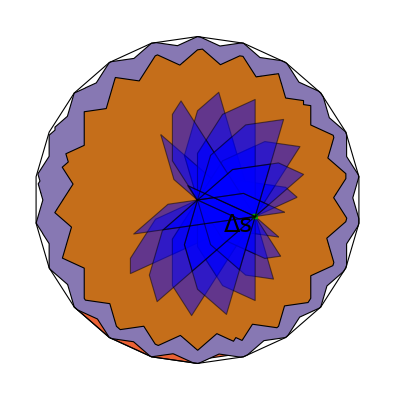

```mathematica
sides =11;
v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];
vcopy=Insert[v,{1,0},1];
vCF = calculateDeltaConfig[v];
ps1={0.1,0.3};
ps2={0.8,0.1};
{p2,p1}=deltaToTwoConfigs[vcopy,ps2-ps1];
TotalReaSet=boundaryPt3[vcopy,p2,p1];
TotalReaSetOld=boundaryPt2[vcopy,p2,p1];
edgepts2 = Chop[First[TotalReaSet]];
(*4-move*)
polys4temp=Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =boundaryPt3[vcopy,p2,p1]
,{pt,.999*Chop[cleanPoly2[cleanPoly[edgepts2]]]}];
polys4=RegionUnion@@polys4temp;
(*6-move*)
edgepts4 =Chop[First@polys4];
polys6temp=Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =boundaryPt3[vcopy,p2,p1]
,{pt,.999*Chop[cleanPoly2[cleanPoly[edgepts4]]]}];
polys6=RegionUnion@@polys6temp;
(*8-move*)
If[sides > 8,
edgepts6 =Chop[First@polys6];
polys8temp=Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =boundaryPt3[vcopy,p2,p1]
,{pt,.999*Chop[cleanPoly2[cleanPoly[edgepts6]]]}];
polys8=RegionUnion@@polys8temp;
]

Graphics[{
If[sides > 8,
(*8-move*){ColorData[97,"ColorList"]⟦4⟧,EdgeForm[Black],polys8}],
(*6-move*){ColorData[97,"ColorList"]⟦5⟧,EdgeForm[Black],polys6},
(*4-move*){ColorData[97,"ColorList"]⟦6⟧,EdgeForm[Black],polys4},
(*(*2-move*){Lighter[Blue],EdgeForm[Black],Polygon[edgepts2]},*)
{Blue, Opacity[0.5],EdgeForm[Black],Polygon[TotalReaSetOld]},
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
}]
```

```mathematica
polys4temp=Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =boundaryPt3[vcopy,p2,p1]
,{pt,.999*Chop[cleanPoly2[cleanPoly[edgepts2]]]}];
```

```mathematica
edgepts2
```

```mathematica
(*20 sided*)
edgepts2  ={{0.7000000000000001,-0.2},{0.92,-0.165},{0.897,-0.14200000000000002},{0.8554788732394366,-0.12086738351254485},{0.979,-0.058},{1.1340000000000001,0.021},{0.9929916201117318,0.09299162011173188},{0.993,0.093},{1.214,0.314},{1.118,0.363},{0.9967404972452429,0.3822288531876476},{1.139,0.661},{0.9510000000000001,0.6910000000000001},{0.8381717333029145,0.6731081389380027},{0.887,0.982},{0.6910000000000001,0.9510000000000001},{0.5307786121911937,0.8694536305775968},{0.482,1.178},{0.363,1.118},{0.14200000000000002,0.897},{0.14176828539673772,0.8965447297583791},{0,1.175},{-0.14200000000000002,0.897},{-0.17690223463687152,0.6769022346368715},{-0.177,0.677},{-0.375,0.875},{-0.389,0.786},{-0.34,0.47700000000000004},{-0.198,0.198},{0,0},{-0.00032326944085811493,-0.00016453140000662753},{-0.22,-0.035},{-0.499,-0.177},{-0.72,-0.398},{-0.735,-0.427},{-0.5148686806471171,-0.3922138162010259},{-0.642,-0.642},{-0.684,-0.905},{-0.4049737272866887,-0.7628354827714079},{-0.405,-0.763},{-0.40467961625958254,-0.7628367637594072},{-0.41200000000000003,-0.809},{-0.363,-1.118},{-0.314,-1.214},{-0.09309263657957245,-0.9930926365795725},{0,-1.176},{0.134,-1.31},{0.2762342629482072,-1.0312342629482072},{0.363,-1.118},{0.54,-1.208},{0.589050895945119,-0.8991119255347918},{0.6910000000000001,-0.9510000000000001},{0.8220000000000001,-0.972},{0.7732622727959317,-0.6628826343084437},{0.9500000000000001,-0.6910000000000001},{0.842,-0.47900000000000004},{0.8078907995036341,-0.41198262719376},{0.808,-0.41200000000000003},{0.8079121163810283,-0.41182748771090744},{0.809,-0.41200000000000003},{0.898,-0.398}}
```

```mathematica
Plot[polys4temp]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[polys4temp]

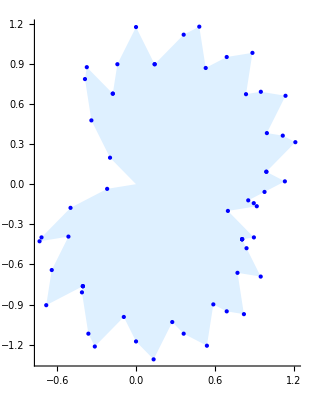

```mathematica
Graphics[{LightBlue,Polygon[edgepts2],Blue,Point[cleanPoly[edgepts2]]},Axes->True]
```

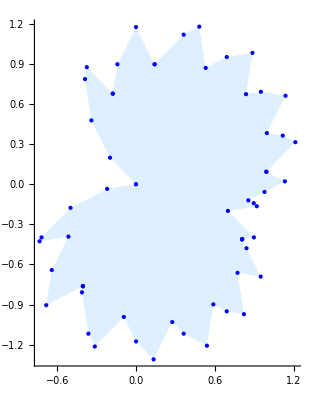

```mathematica
Graphics[{LightBlue,Polygon[edgepts2],Blue,Point[edgepts2]},Axes->True]
```

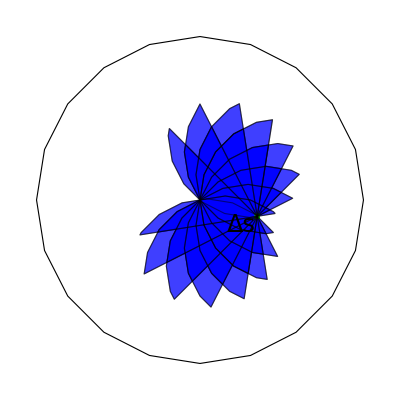

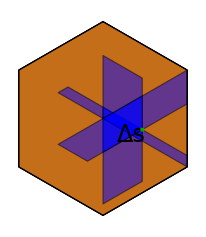
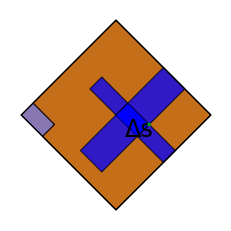
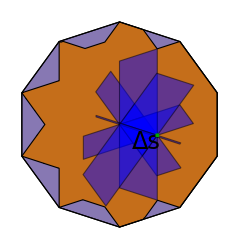
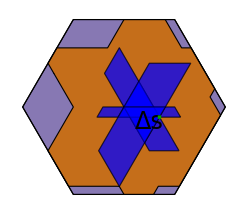
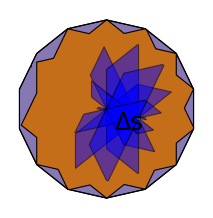
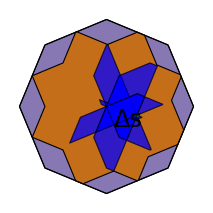
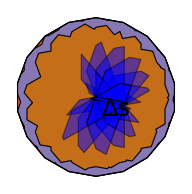

#### Polygons with 3, 4, 5, 6, 7, 8, 9, 10, 11,and 12 and 14 (?) sides. The two - move reachable $\Delta$ configurations are in transparent blue polygons. The four - move set is brown, the six - move set is purple, and the eight - move set is pink. As the corner angle increases, more moves are required to reach all possible configurations. All $\Delta$ - configurations are reachable in two moves for a three - sided polygon. Polygons with less than nine sides can be reached in four - moves.

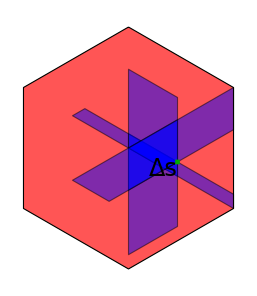
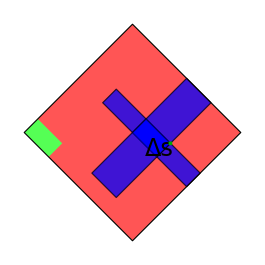
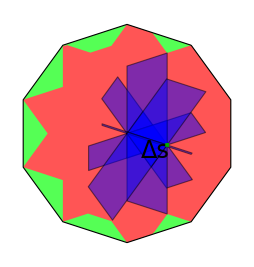
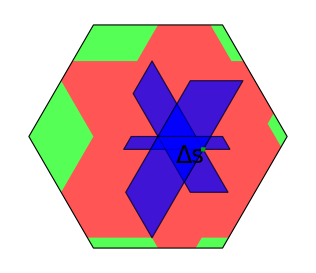
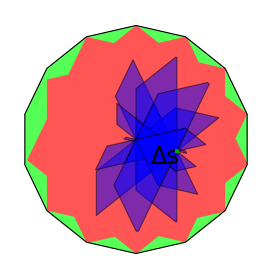
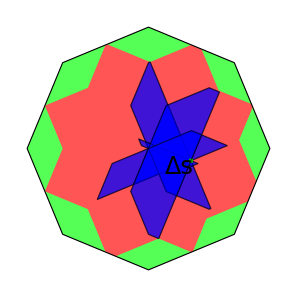
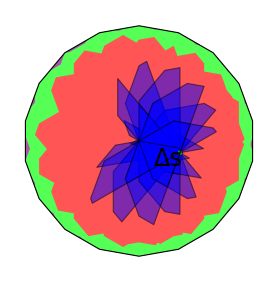
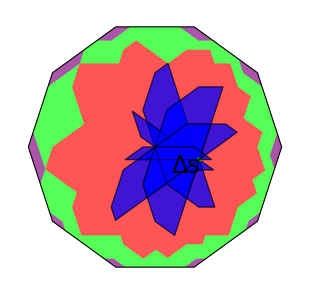
```mathematica
3,4,5,6,7,8,9,10,20  -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

## Shiva : This code doesn’t work... It is a slight approximation, and only works for less than 6 sides.

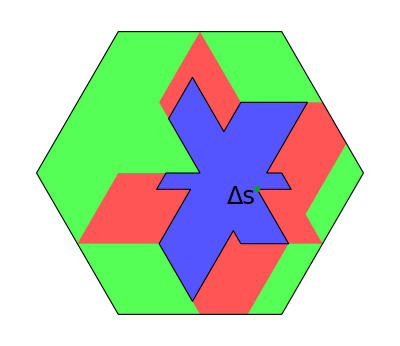

```mathematica
sides =6;
v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];
vcopy=Insert[v,{1,0},1];
vCF = calculateDeltaConfig[v];
ps1={0.1,0.3};
ps2={0.8,0.1};
{p2,p1}=deltaToTwoConfigs[vcopy,ps2-ps1];
TotalReaSet=boundaryPt2[vcopy,p2,p1];
edgepts2 = Chop[First[RegionUnion@@Polygon/@TotalReaSet]];
(*4-move*)
polys4temp=DeleteCases[Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =DeleteCases[Chop[boundaryPt2[vcopy,p2,p1]],{}]
(*RegionUnion@@Polygon/@rset*)
,{pt,.999*Chop[edgepts2]}],{}];
polys4=RegionUnion@@Chop[Table[RegionUnion@@Polygon/@ cleanPoly/@polysv,{polysv,polys4temp}]];
polys4=Polygon[cleanPoly2[First@polys4]];
edgepts4 =cleanPoly2[Partition[Flatten[First@polys4],2]];
(*6-move*)
polys6temp=DeleteCases[Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =DeleteCases[Chop[boundaryPt2[vcopy,p2,p1]],{}]
(*RegionUnion@@Polygon/@rset*)
,{pt,.999*Chop[edgepts4]}],{}];

polys6=RegionUnion@@Chop[Table[RegionUnion@@Polygon/@ cleanPoly/@polysv,{polysv,polys6temp}]];
polys6=Polygon[cleanPoly2[First@polys6]];

Graphics[{
(*6-move*){Lighter[Green],EdgeForm[None],polys6},
(*4-move*){Lighter[Red],EdgeForm[None],polys4},
(*2-move*){Lighter[Blue],EdgeForm[Black],Polygon[edgepts2]},
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
}]
```

## Shiva : this code will generate the shapes, but it is not optimized code. I want to combine the polygons, because the images generated are huge!. You can Rasterize[ ] them.

```mathematica
sides =6;
v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];
vcopy=Insert[v,{1,0},1];
vCF = calculateDeltaConfig[v];
ps1={0.1,0.3};
ps2={0.8,0.1};
{p2,p1}=deltaToTwoConfigs[vcopy,ps2-ps1];
TotalReaSet=boundaryPt2[vcopy,p2,p1];
edgepts2 = Chop[First[RegionUnion@@Polygon/@TotalReaSet]];
(*4-move*)
polys4=DeleteCases[Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =DeleteCases[Chop[boundaryPt2[vcopy,p2,p1]],{}]
(*RegionUnion@@Polygon/@rset*)
,{pt,.999*Chop[edgepts2]}],{}];
edgepts4 =DeleteDuplicates[Partition[Flatten[polys4],2]];
(*6-move*)
polys6=DeleteCases[Table[
{p2,p1}=deltaToTwoConfigs[vcopy,pt];
rset =DeleteCases[Chop[boundaryPt2[vcopy,p2,p1]],{}]
(*RegionUnion@@Polygon/@rset*)
,{pt,.999*Chop[edgepts4]}],{}];

Graphics[{
(*6-move*){Lighter[Green],EdgeForm[None],Table[Polygon[polysv],{polysv,polys6}]},
(*4-move*){Lighter[Red],EdgeForm[None],Table[Polygon[polysv],{polysv,polys4}]},
(*2-move*){Lighter[Blue],EdgeForm[Black],Polygon[edgepts2]},
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
}]
```

-Graphics-

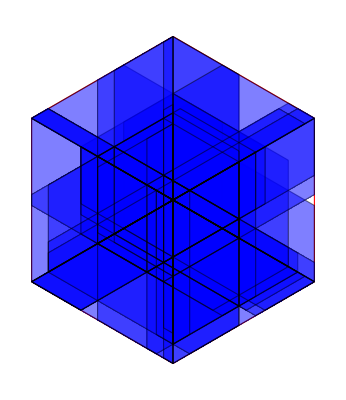

```mathematica
Graphics[{{EdgeForm[Red],FaceForm[None],Polygon[vCF]},Opacity[0.5],Blue,EdgeForm[Black],Table[Polygon[polysv],{polysv,polys}]}]
```

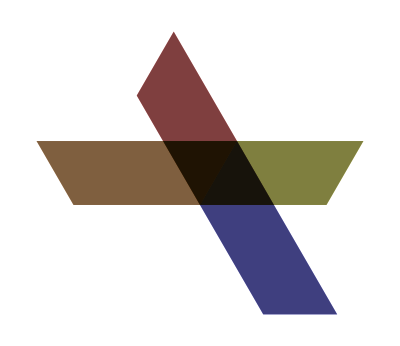

```mathematica
Graphics[{Opacity[0.5],Red,
Polygon[{{0.29223574658372925,0.5061671608708425},{0.5844714931674586,0},{0,0},{-0.5,0.8660254037844386},{-0.20776425341627047,1.3721925646552813},{-0.2077642534162707,1.372192564655281}}],
Blue,
Polygon[{{0.7922357465837292,-0.35985824291359614},{1.0844714931674586,-0.8660254037844386},{0.49999999999999994,-0.8660254037844386},{0,0},{0.29223574658372947,0.5061671608708426},{0.29223574658372925,0.5061671608708425}}],
Yellow,
Polygon[{{0.29223574658372925,0.5061671608708425},{-0.2922357465837296,0.5061671608708425},{0,0},{1.,0},{1.2922357465837295,0.5061671608708425},{1.2922357465837293,0.5061671608708425}}],
Orange,
Polygon[{{-0.7077642534162707,0.5061671608708425},{-1.2922357465837295,0.5061671608708425},{-1.,0},{0,0},{0.29223574658372947,0.5061671608708425},{0.29223574658372925,0.5061671608708425}}],
Black,
Polygon[{{0.29223574658372925,0.5061671608708425},{0.29223574658372947,0.5061671608708426},{0,0},{0.49999999999999994,-0.8660254037844386},{1.0844714931674586,-0.8660254037844386},{0.7922357465837292,-0.35985824291359614}}],Polygon[{{-0.2077642534162707,1.372192564655281},{-0.20776425341627047,1.3721925646552813},{-0.5,0.8660254037844386},{0,0},{0.5844714931674586,0},{0.29223574658372925,0.5061671608708425}}],Polygon[{{0.29223574658372925,0.5061671608708425},{-0.2922357465837296,0.5061671608708425},{0,0},{1.,0},{1.2922357465837295,0.5061671608708425},{1.2922357465837293,0.5061671608708425}}],Polygon[{{-0.7077642534162707,0.5061671608708425},{-1.2922357465837295,0.5061671608708425},{-1.,0},{0,0},{0.29223574658372947,0.5061671608708425},{0.29223574658372925,0.5061671608708425}}]
}]
```

```mathematica
Polygon/@polys⟦4⟧
```

{Polygon[{{0.49995,0.865939},{0.9999,0},{0,0},{-0.5,0.866025},{-0.00005,1.73196},{-0.00005,1.73196}}],Polygon[{{0.99995,-0.0000866025},{1.4999,-0.866025},{0.5,-0.866025},{0,0},{0.49995,0.865939},{0.49995,0.865939}}],Polygon[{{0.49995,0.865939},{-0.49995,0.865939},{0,0},{1.,0},{1.49995,0.865939},{1.49995,0.865939}}],Polygon[{{-0.50005,0.865939},{-1.49995,0.865939},{-1.,0},{0,0},{0.49995,0.865939},{0.49995,0.865939}}],Polygon[{{0.49995,0.865939},{0.49995,0.865939},{0,0},{0.5,-0.866025},{1.4999,-0.866025},{0.99995,-0.0000866025}}],Polygon[{{-0.00005,1.73196},{-0.00005,1.73196},{-0.5,0.866025},{0,0},{0.9999,0},{0.49995,0.865939}}],Polygon[{{0.49995,0.865939},{-0.49995,0.865939},{0,0},{1.,0},{1.49995,0.865939},{1.49995,0.865939}}],Polygon[{{-0.50005,0.865939},{-1.49995,0.865939},{-1.,0},{0,0},{0.49995,0.865939},{0.49995,0.865939}}]}

```mathematica
Chop[RegionUnion@@Polygon/@DeleteDuplicates[polys⟦5⟧]]
```

MeshRegion::dgcellr: Degenerate cells including Polygon[{7,5,6}] have been removed.

MeshRegion::dgcellr: Degenerate cells including Polygon[{4,5,6}] have been removed.

General::stop: Further output of MeshRegion::dgcellr will be suppressed during this calculation.

Polygon[{{0.584471,0},{1.,0},{1.29224,0.506167},{0.292236,0.506167},{-0.207764,1.37219},{-0.5,0.866025},{-0.292236,0.506167},{-0.707764,0.506167},{-1.29224,0.506167},{-1.,0},{0,0},{0.5,-0.866025},{1.08447,-0.866025},{0.792236,-0.359858}}]

```mathematica
Chop[-5.551115123125783*^-17]
```

0

```mathematica
RegionUnion@@Flatten[Polygon/@polys⟦4⟧]
```

MeshRegion::dgcellr: Degenerate cells including Polygon[{4,6,5}] have been removed.

MeshRegion::dgcellr: Degenerate cells including Polygon[{3,1,2}] have been removed.

General::stop: Further output of MeshRegion::dgcellr will be suppressed during this calculation.

Polygon[{{0.999,0.},{1.,0.},{1.4995,0.865159},{0.4995,0.865159},{-0.0005,1.73118},{-0.5,0.866025},{-0.4995,0.865159},{-0.5005,0.865159},{-1.4995,0.865159},{-1.,0.},{0.,0.},{0.5,-0.866025},{1.499,-0.866025},{0.9995,-0.000866025}}]

```mathematica
Chop[Round[polys⟦4⟧,.1]]
```

```mathematica
{{{0.5,0.9},{1.,0.},{0.,0.},{-0.5,0.9},{0.,1.7000000000000002},{0.,1.7000000000000002}},
{{1.,0.},{1.5,-0.9},{0.5,-0.9},{0.,0.},{0.5,0.9},{0.5,0.9}},
{{0.5,0.9},{-0.5,0.9},{0.,0.},{1.,0.},{1.5,0.9},{1.5,0.9}},
{{-0.5,0.9},{-1.5,0.9},{-1.,0.},{0.,0.},{0.5,0.9},{0.5,0.9}},
{{0.5,0.9},{0.5,0.9},{0.,0.},{0.5,-0.9},{1.5,-0.9},{1.,0.}},
{{0.,1.7000000000000002},{0.,1.7000000000000002},{-0.5,0.9},{0.,0.},{1.,0.},{0.5,0.9}},
{{0.5,0.9},{-0.5,0.9},{0.,0.},{1.,0.},{1.5,0.9},{1.5,0.9}},
{{-0.5,0.9},{-1.5,0.9},{-1.,0.},{0.,0.},{0.5,0.9},{0.5,0.9}}}
```

```mathematica
{{{0.4995,0.8651593783806542},{0.9989999999999997,0},{0,0},{-0.5,0.8660254037844386},{-0.0004999999999998339,1.731184782165093},{-0.0004999999999999449,1.7311847821650928}},
{{0.9994999999999999,-0.0008660254037844428},{1.4989999999999997,-0.8660254037844386},{0.49999999999999994,-0.8660254037844386},{0,0},{0.4995000000000001,0.8651593783806545},{0.4995,0.8651593783806542}},{{0.4995,0.8651593783806542},{-0.4995000000000001,0.8651593783806542},{0,0},{1.,0},{1.4995,0.8651593783806542},{1.4995,0.8651593783806542}},{{-0.5005,0.8651593783806542},{-1.4995,0.8651593783806542},{-1.,0},{0,0},{0.4995,0.8651593783806542},{0.4995,0.8651593783806542}},{{0.4995,0.8651593783806542},{0.4995000000000001,0.8651593783806545},{0,0},{0.49999999999999994,-0.8660254037844386},{1.4989999999999997,-0.8660254037844386},{0.9994999999999999,-0.0008660254037844428}},{{-0.0004999999999999449,1.7311847821650928},{-0.0004999999999998339,1.731184782165093},{-0.5,0.8660254037844386},{0,0},{0.9989999999999997,0},{0.4995,0.8651593783806542}},{{0.4995,0.8651593783806542},{-0.4995000000000001,0.8651593783806542},{0,0},{1.,0},{1.4995,0.8651593783806542},{1.4995,0.8651593783806542}},{{-0.5005,0.8651593783806542},{-1.4995,0.8651593783806542},{-1.,0},{0,0},{0.4995,0.8651593783806542},{0.4995,0.8651593783806542}}}
```

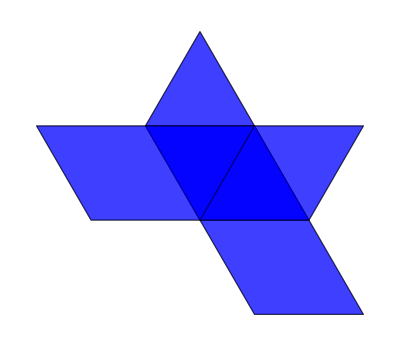

```mathematica
Graphics[{Opacity[0.5],Blue,EdgeForm[Black],Polygon[polys⟦4⟧]}]
```

```mathematica
RegionUnion@@Polygon/@polys⟦4⟧
```

MeshRegion::dgcellr: Degenerate cells including Polygon[{4,6,5}] have been removed.

MeshRegion::dgcellr: Degenerate cells including Polygon[{3,1,2}] have been removed.

General::stop: Further output of MeshRegion::dgcellr will be suppressed during this calculation.

Polygon[{{0.999,0.},{1.,0.},{1.4995,0.865159},{0.4995,0.865159},{-0.0005,1.73118},{-0.5,0.866025},{-0.4995,0.865159},{-0.5005,0.865159},{-1.4995,0.865159},{-1.,0.},{0.,0.},{0.5,-0.866025},{1.499,-0.866025},{0.9995,-0.000866025}}]

MeshRegion::dgcellr: Degenerate cells including Polygon[{4,6,5}] have been removed.

MeshRegion::dgcellr: Degenerate cells including Polygon[{3,1,2}] have been removed.

General::stop: Further output of MeshRegion::dgcellr will be suppressed during this calculation.

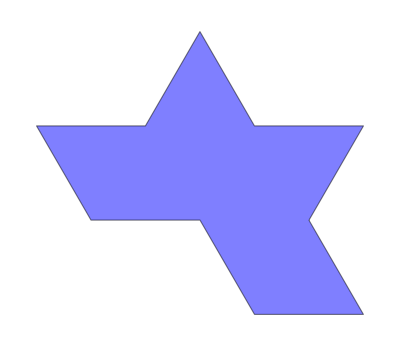

```mathematica
Graphics[{Opacity[0.5],Blue,EdgeForm[Black],RegionUnion@@Polygon/@polys⟦4⟧}]
```

```mathematica
Graphics[{Opacity[0.5],Blue,EdgeForm[Black],Polygon[polys⟦4⟧]}]
```

-Graphics-

```mathematica
RegionUnion[Polygon[{{0.7000000000000001,-0.19999999999999998},{0.7000000000000001,-0.19999999999999998},{0.7000000000000001,-0.40414518843273817},{-0.7999999999999999,0.46188021535170043},{-0.6232050807568877,0.5639528095680695},{-0.09999999999999987,0.2618802153517005}}],Polygon[{{1.5,-0.6618802153517004},{1.5,-0.6618802153517004},{1.5,-0.8660254037844386},{0.,0.},{0.1767949192431122,0.10207259421636902},{0.7000000000000001,-0.19999999999999998}}]]
```

Polygon[{{0.7,-0.404145},{1.5,-0.866025},{1.5,-0.66188},{0.7,-0.2},{0.176795,0.102073},{-0.1,0.26188},{-0.623205,0.563953},{-0.8,0.46188},{0.,0.}}]

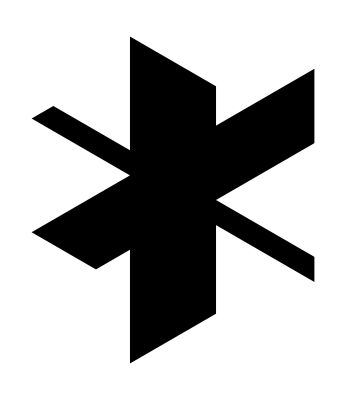

```mathematica
Graphics[RegionUnion@@Polygon/@TotalReaSet]
```

```mathematica
sides =3;
v=Table[{Cos[2 (π n)/sides],Sin[2 (π n)/sides]},{n,1,sides}];
vcopy=Insert[v,{1,0},1];
vCF = calculateDeltaConfig[v];
ps1={0.1,0.3};
ps2={0.8,0.1};
{p2,p1}=deltaToTwoConfigs[vcopy,ps2-ps1];
TotalReaSet3=boundaryPt3[vcopy,p2,p1];
TotalReaSet=boundaryPt2[vcopy,p2,p1];
(*Table[Graphics[{
(*2-move*){Lighter[Blue],EdgeForm[Black],Polygon[TotalReaSet[[i]]]},
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
Text[i,{0,2}]
}],{i,Length[TotalReaSet]}]*)
Length[First@TotalReaSet3]
Graphics[{
(*2-move*){Lighter[Blue],EdgeForm[Black],Polygon[TotalReaSet]},
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
Text[i,{0,2}]
}]
Graphics[{
(*2-move*){Lighter[Blue],EdgeForm[Black],TotalReaSet3},
Red, PointSize[Medium],Point[Last[TotalReaSet3]],
(*Edge*){EdgeForm[Black],FaceForm[None],Polygon[vCF]},
r = 1/40;
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],
Text[Style[StringForm["Δs"],Italic, FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧- 0.2,ps2⟦2⟧-ps1⟦2⟧-0.1}],
Text[i,{0,2}]
}]
```